```mathematica
a={1,2,3}
;
```

{1,2,3}

```mathematica
□^□
```

```mathematica
Sin[2]
```

Sin[2]

```mathematica
;
Sin[1];
```

Syntax::sntxi: Incomplete expression; more input is needed "".

```mathematica
a={1,2,3}
Head[a]
```

{1,2,3}

List

```mathematica
Head[Sin[1.9]]
```

Real

```mathematica
Part[{1,2,3},2]
```

2

```mathematica
Head[{1,2,3}]
```

List

```mathematica
Factorize 34
```

34 Factorize

```mathematica
Factorize[24
]
```

Factorize[24]

```mathematica
Graphics[{PointSize[.02],Point[{1,4}],Line[{{1,4},{2,5}}],Point[{2,5}]}]/.{1->2,2->1}
```

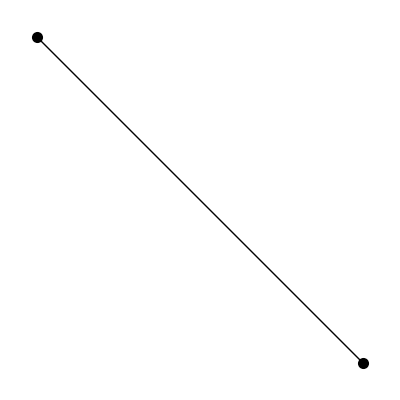

```mathematica
Count[IdentityMatrix[4],{1,0,0,0},{1}]
```

1

```mathematica
({{1, x, x, x}, {x, 1, x, x}, {x, x, 1, x}, {x, x, x, 1}})




clear
```

{{1,x,x,x},{x,1,x,x},{x,x,1,x},{x,x,x,1}}

clear

```mathematica
clear;
```

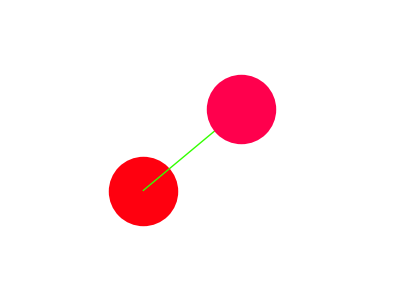

```mathematica
Graphics[{Hue[.99],PointSize[.2],Point[{1,4}],Hue[.3],Line[{{1,4},{2,5}}],Hue[.95],Point[{2,5}]},PlotRange->{{-1,3},{3,6}}]/.{1->.3,2->1.5}
```

```mathematica
Graphics[{Hue[2],PointSize[.2],Point[{1,4}],Hue[.3],Line[{{1,4},{2,5}}],Hue[.95],Point[{2,5}]},PlotRange->{{-1,3},{3,6}}]/.{1->.3,2->1.5}
```

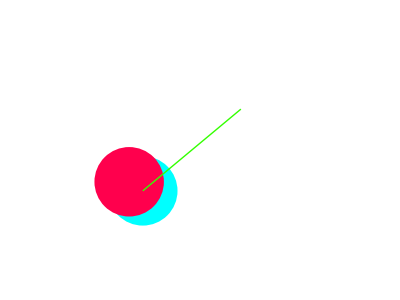

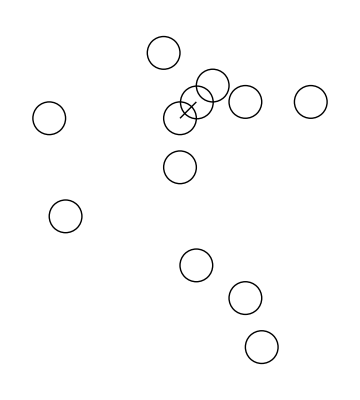

```mathematica
Graphics[{PointSize[.02],Point[{9,5}],Point[{2,-5}],Point[{5,5}],Point[{3,6}],Point[{1,1}],Point[{5,-7}],Point[{-7,4}],Point[{6,-10}],Point[{-6,-2}],Point[{0,8}],Point[{1,4}],Line[{{1,4},{2,5}}],Point[{2,5}]},AspectRatio->Automatic]/.{Point->Circle}
```

```mathematica
g:=#^2&
```

```mathematica
g[4]
```

16

```mathematica
FullForm[g]
```

Function[Power[Slot[1],2]]

```mathematica
Head[%]
```

Function

```mathematica
#1*(#2+#3)&[3,4,5]
```

27

```mathematica
Map[g,{2,3,4}]
```

{4,9,16}

```mathematica
a=RandomInteger[{1,5},{3,3}]//MatrixForm
```

(3 | 4 | 4
5 | 5 | 5
2 | 5 | 3)

```mathematica
Apply[Union,a]
```

{{2,5,3},{3,4,4},{5,5,5}}

```mathematica
Total/@a
```

(10
14
12)

```mathematica
Union@@a
```

{{2,5,3},{3,4,4},{5,5,5}}

```mathematica
Union/@a
```

```mathematica
({{2, 5, 3}, {3, 4, 4}, {5, 5, 5}})
```

{{2,5,3},{3,4,4},{5,5,5}}

```mathematica
Map[Total,a]
```

(10
14
12)

```mathematica
Map[Union,a]
```

(2 | 5 | 3
3 | 4 | 4
5 | 5 | 5)

```mathematica
Apply[Union,a]
```

{{2,5,3},{3,4,4},{5,5,5}}

```mathematica
a
```

(3 | 4 | 4
5 | 5 | 5
2 | 5 | 3)

```mathematica
Union[a]
```

(3 | 4 | 4
5 | 5 | 5
2 | 5 | 3)

```mathematica
a
```

(3 | 4 | 4
5 | 5 | 5
2 | 5 | 3)

```mathematica
a//ListForm
```

ListForm[(3 | 4 | 4
5 | 5 | 5
2 | 5 | 3)]

```mathematica
b=RandomInteger[{1,5},{3,3}]
```

{{1,4,5},{1,3,5},{1,5,3}}

```mathematica
Total/@b
```

{10,9,9}

```mathematica
Union@@b
```

{1,3,4,5}

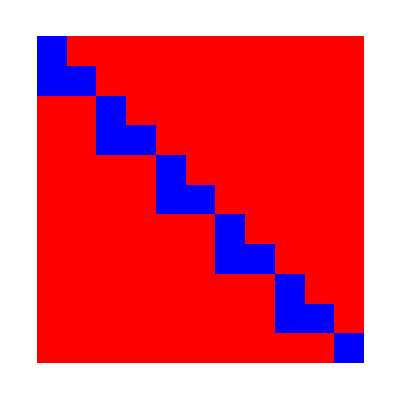

```mathematica
ArrayPlot[CellularAutomaton[20,{{1},0},10],ColorRules->{1->Blue,0->Red}]
```

```mathematica
ArrayPlot[CellularAutomaton[{9,2,{{-1},{2}}},{{1},0},5]]
```

```mathematica
l:=CellularAutomaton[{9,2,{{-1},{2}}},{{1},0},50]
```

```mathematica
Length[l]
```

51

```mathematica
1[0]
```

1[0]

```mathematica
l[[2]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Head[l]
```

```mathematica
List

Tail[l]
```

List

Tail[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1},{1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1},{1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,1},{1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1},{1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1},{0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0}}]

```mathematica
Length[Tail]
```

```mathematica
0
```

```mathematica
Count[l[[4]],1]
```

147

```mathematica
Do[Count[l[[i]],1],{0,Length[l]}]
```

Do::itraw: Raw object 0 cannot be used as an iterator.

```mathematica
a [i]:=Do[Count[l⟦i⟧,1],{i,0,2,1}]
```

SetDelayed::write: Tag Null in Null[i] is Protected.

$Failed

```mathematica
SameQ@@f[c,d,a,b]
```

```mathematica
False
```

```mathematica
SameQ/@f[c,d,a,b]
```

f[True,True,True,True]

```mathematica
SameQ[F[a]]
```

True

```mathematica
Table[CellularAutomaton[{744,{3,1}},{IntegerDigits[n,3],0},10],{n,10}]
```

{{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,1,2,1,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,2,0,0,0,0,0,2,2,2,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,2,2,1,2,1,2,2,0,2,2,1,2,1,2,2,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1}},{{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,1,0,1,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,1,1,1,1,1,1,0,1,0,0,0,0,0},{0,0,0,0,2,2,1,1,0,0,0,0,0,1,1,2,2,0,0,0,0},{0,0,0,1,0,0,0,1,2,0,0,0,2,1,0,0,0,1,0,0,0},{0,0,2,2,2,0,2,0,0,1,0,1,0,0,2,0,2,2,2,0,0},{0,1,0,1,0,0,1,1,2,2,1,2,2,1,1,0,0,1,0,1,0},{2,2,1,2,2,2,1,0,0,0,0,0,0,0,1,2,2,2,1,2,2}},{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,1,2,1,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,2,0,0,0,0,0,2,2,2,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,2,2,1,2,1,2,2,0,2,2,1,2,1,2,2,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1}},{{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,1,1,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,2,0,0,2,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,1,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,1,2,1,1,1,1,2,1,2,2,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0},{0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0},{0,2,2,1,2,1,2,2,0,0,0,0,0,0,2,2,1,2,1,2,2,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1}},{{0,0,0,0,0,0,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,2,2,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,1,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,2,0,2,2,1,2,2,0,0,0,0,0,0},{0,0,0,0,0,2,2,2,1,1,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,1,2,0,0,0,0,2,2,2,0,0,0,0},{0,0,0,2,2,1,2,2,2,0,0,1,0,0,1,0,1,0,1,0,0,0},{0,0,1,0,0,0,0,1,0,1,2,2,2,2,2,1,2,1,2,2,0,0},{0,2,2,2,0,0,2,2,1,0,0,1,1,1,0,0,0,0,0,0,1,0},{1,0,1,0,1,1,0,0,0,2,2,1,0,1,2,0,0,0,0,2,2,2}},{{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,1,0,1,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,1,1,1,1,1,1,0,1,0,0,0,0,0},{0,0,0,0,2,2,1,1,0,0,0,0,0,1,1,2,2,0,0,0,0},{0,0,0,1,0,0,0,1,2,0,0,0,2,1,0,0,0,1,0,0,0},{0,0,2,2,2,0,2,0,0,1,0,1,0,0,2,0,2,2,2,0,0},{0,1,0,1,0,0,1,1,2,2,1,2,2,1,1,0,0,1,0,1,0},{2,2,1,2,2,2,1,0,0,0,0,0,0,0,1,2,2,2,1,2,2}},{{0,0,0,0,0,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,2,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,1,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,2,1,2,2,0,2,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,1,1,2,2,2,0,0,0,0,0},{0,0,0,0,2,2,2,0,0,0,0,2,1,0,0,1,0,1,0,0,0,0},{0,0,0,1,0,1,0,1,0,0,1,0,0,2,2,2,1,2,2,0,0,0},{0,0,2,2,1,2,1,2,2,2,2,2,1,0,1,0,0,0,0,1,0,0},{0,1,0,0,0,0,0,0,1,1,1,0,0,1,2,2,0,0,2,2,2,0},{2,2,2,0,0,0,0,2,1,0,1,2,2,0,0,0,1,1,0,1,0,1}},{{0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,2,2,2,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,1,1,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,2,1,1,0,0,1,1,2,2,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,2,2,1,0,0,0,1,0,0,0,0,0},{0,0,0,0,2,2,2,0,2,0,0,0,0,2,0,2,2,2,0,0,0,0},{0,0,0,1,0,1,0,0,1,1,0,0,1,1,0,0,1,0,1,0,0,0},{0,0,2,2,1,2,2,2,1,1,2,2,1,1,2,2,2,1,2,2,0,0},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{2,2,2,0,0,2,2,2,0,0,0,0,0,0,2,2,2,0,0,2,2,2}},{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,1,2,1,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,2,0,0,0,0,0,2,2,2,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,2,2,1,2,1,2,2,0,2,2,1,2,1,2,2,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1}},{{0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,2,1,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,2,0,0,0,2,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,1,2,1,2,1,2,1,2,1,2,2,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0},{0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0},{0,2,2,1,2,1,2,2,0,0,0,0,0,0,0,2,2,1,2,1,2,2,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1}}}

```mathematica
%
```

{{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,1,2,1,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,2,0,0,0,0,0,2,2,2,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,2,2,1,2,1,2,2,0,2,2,1,2,1,2,2,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1}},{{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,1,0,1,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,1,1,1,1,1,1,0,1,0,0,0,0,0},{0,0,0,0,2,2,1,1,0,0,0,0,0,1,1,2,2,0,0,0,0},{0,0,0,1,0,0,0,1,2,0,0,0,2,1,0,0,0,1,0,0,0},{0,0,2,2,2,0,2,0,0,1,0,1,0,0,2,0,2,2,2,0,0},{0,1,0,1,0,0,1,1,2,2,1,2,2,1,1,0,0,1,0,1,0},{2,2,1,2,2,2,1,0,0,0,0,0,0,0,1,2,2,2,1,2,2}},{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,1,2,1,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,2,0,0,0,0,0,2,2,2,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,2,2,1,2,1,2,2,0,2,2,1,2,1,2,2,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1}},{{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,1,1,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,2,0,0,2,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,1,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,1,2,1,1,1,1,2,1,2,2,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0},{0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0},{0,2,2,1,2,1,2,2,0,0,0,0,0,0,2,2,1,2,1,2,2,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1}},{{0,0,0,0,0,0,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,2,2,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,1,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,2,0,2,2,1,2,2,0,0,0,0,0,0},{0,0,0,0,0,2,2,2,1,1,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,1,2,0,0,0,0,2,2,2,0,0,0,0},{0,0,0,2,2,1,2,2,2,0,0,1,0,0,1,0,1,0,1,0,0,0},{0,0,1,0,0,0,0,1,0,1,2,2,2,2,2,1,2,1,2,2,0,0},{0,2,2,2,0,0,2,2,1,0,0,1,1,1,0,0,0,0,0,0,1,0},{1,0,1,0,1,1,0,0,0,2,2,1,0,1,2,0,0,0,0,2,2,2}},{{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,1,0,1,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,1,1,1,1,1,1,0,1,0,0,0,0,0},{0,0,0,0,2,2,1,1,0,0,0,0,0,1,1,2,2,0,0,0,0},{0,0,0,1,0,0,0,1,2,0,0,0,2,1,0,0,0,1,0,0,0},{0,0,2,2,2,0,2,0,0,1,0,1,0,0,2,0,2,2,2,0,0},{0,1,0,1,0,0,1,1,2,2,1,2,2,1,1,0,0,1,0,1,0},{2,2,1,2,2,2,1,0,0,0,0,0,0,0,1,2,2,2,1,2,2}},{{0,0,0,0,0,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,2,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,1,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,2,1,2,2,0,2,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,1,1,2,2,2,0,0,0,0,0},{0,0,0,0,2,2,2,0,0,0,0,2,1,0,0,1,0,1,0,0,0,0},{0,0,0,1,0,1,0,1,0,0,1,0,0,2,2,2,1,2,2,0,0,0},{0,0,2,2,1,2,1,2,2,2,2,2,1,0,1,0,0,0,0,1,0,0},{0,1,0,0,0,0,0,0,1,1,1,0,0,1,2,2,0,0,2,2,2,0},{2,2,2,0,0,0,0,2,1,0,1,2,2,0,0,0,1,1,0,1,0,1}},{{0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,2,2,2,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,1,1,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,2,1,1,0,0,1,1,2,2,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,2,2,1,0,0,0,1,0,0,0,0,0},{0,0,0,0,2,2,2,0,2,0,0,0,0,2,0,2,2,2,0,0,0,0},{0,0,0,1,0,1,0,0,1,1,0,0,1,1,0,0,1,0,1,0,0,0},{0,0,2,2,1,2,2,2,1,1,2,2,1,1,2,2,2,1,2,2,0,0},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{2,2,2,0,0,2,2,2,0,0,0,0,0,0,2,2,2,0,0,2,2,2}},{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,1,2,1,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,2,0,0,0,0,0,2,2,2,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,2,2,1,2,1,2,2,0,2,2,1,2,1,2,2,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1}},{{0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,2,1,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,2,0,0,0,2,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,1,2,1,2,1,2,1,2,1,2,2,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0},{0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0},{0,2,2,1,2,1,2,2,0,0,0,0,0,0,0,2,2,1,2,1,2,2,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1}}}

```mathematica
%[2]
```

{{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,1,2,1,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,2,0,0,0,0,0,2,2,2,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,2,2,1,2,1,2,2,0,2,2,1,2,1,2,2,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1}},{{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,1,0,1,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,1,1,1,1,1,1,0,1,0,0,0,0,0},{0,0,0,0,2,2,1,1,0,0,0,0,0,1,1,2,2,0,0,0,0},{0,0,0,1,0,0,0,1,2,0,0,0,2,1,0,0,0,1,0,0,0},{0,0,2,2,2,0,2,0,0,1,0,1,0,0,2,0,2,2,2,0,0},{0,1,0,1,0,0,1,1,2,2,1,2,2,1,1,0,0,1,0,1,0},{2,2,1,2,2,2,1,0,0,0,0,0,0,0,1,2,2,2,1,2,2}},{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,1,2,1,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,2,0,0,0,0,0,2,2,2,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,2,2,1,2,1,2,2,0,2,2,1,2,1,2,2,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1}},{{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,1,1,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,2,0,0,2,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,1,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,1,2,1,1,1,1,2,1,2,2,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0},{0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0},{0,2,2,1,2,1,2,2,0,0,0,0,0,0,2,2,1,2,1,2,2,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1}},{{0,0,0,0,0,0,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,1,2,2,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,1,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,2,0,2,2,1,2,2,0,0,0,0,0,0},{0,0,0,0,0,2,2,2,1,1,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,1,2,0,0,0,0,2,2,2,0,0,0,0},{0,0,0,2,2,1,2,2,2,0,0,1,0,0,1,0,1,0,1,0,0,0},{0,0,1,0,0,0,0,1,0,1,2,2,2,2,2,1,2,1,2,2,0,0},{0,2,2,2,0,0,2,2,1,0,0,1,1,1,0,0,0,0,0,0,1,0},{1,0,1,0,1,1,0,0,0,2,2,1,0,1,2,0,0,0,0,2,2,2}},{{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,1,0,1,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,1,1,1,1,1,1,0,1,0,0,0,0,0},{0,0,0,0,2,2,1,1,0,0,0,0,0,1,1,2,2,0,0,0,0},{0,0,0,1,0,0,0,1,2,0,0,0,2,1,0,0,0,1,0,0,0},{0,0,2,2,2,0,2,0,0,1,0,1,0,0,2,0,2,2,2,0,0},{0,1,0,1,0,0,1,1,2,2,1,2,2,1,1,0,0,1,0,1,0},{2,2,1,2,2,2,1,0,0,0,0,0,0,0,1,2,2,2,1,2,2}},{{0,0,0,0,0,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,2,1,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,1,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,2,1,2,2,0,2,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,1,1,2,2,2,0,0,0,0,0},{0,0,0,0,2,2,2,0,0,0,0,2,1,0,0,1,0,1,0,0,0,0},{0,0,0,1,0,1,0,1,0,0,1,0,0,2,2,2,1,2,2,0,0,0},{0,0,2,2,1,2,1,2,2,2,2,2,1,0,1,0,0,0,0,1,0,0},{0,1,0,0,0,0,0,0,1,1,1,0,0,1,2,2,0,0,2,2,2,0},{2,2,2,0,0,0,0,2,1,0,1,2,2,0,0,0,1,1,0,1,0,1}},{{0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,2,2,2,2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,1,1,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,2,1,1,0,0,1,1,2,2,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,2,2,1,0,0,0,1,0,0,0,0,0},{0,0,0,0,2,2,2,0,2,0,0,0,0,2,0,2,2,2,0,0,0,0},{0,0,0,1,0,1,0,0,1,1,0,0,1,1,0,0,1,0,1,0,0,0},{0,0,2,2,1,2,2,2,1,1,2,2,1,1,2,2,2,1,2,2,0,0},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{2,2,2,0,0,2,2,2,0,0,0,0,0,0,2,2,2,0,0,2,2,2}},{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,1,2,1,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,2,0,0,0,0,0,2,2,2,0,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,0,0,1,0,1,0,1,0,0,0,0},{0,0,0,2,2,1,2,1,2,2,0,2,2,1,2,1,2,2,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0},{1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1}},{{0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,2,1,2,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,2,0,0,0,2,2,2,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,2,2,1,2,1,2,1,2,1,2,1,2,2,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0,0},{0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0},{0,2,2,1,2,1,2,2,0,0,0,0,0,0,0,2,2,1,2,1,2,2,0},{1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1}}}[2]

```mathematica
Do[Print[Max@@Table[CellularAutomaton[{744,{3,1}},{IntegerDigits[n,3],0},10],{n,10}][[i]]],{i,10}]
```

2

2

2

«7 more identical outputs»

```mathematica
Do[Print[Count[CellularAutomaton[{744,{3,1}},{{1},0},10][[i]],1]],{i,0,10,1}]
```

0

1

0

3

2

2

0

6

4

2

0

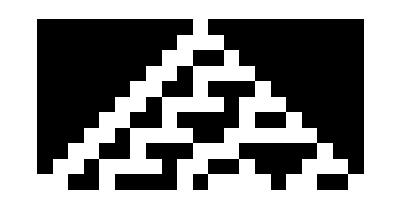

```mathematica
Graphics[Raster[Reverse[CellularAutomaton[30,{{1},0},10]]]]
```

```mathematica
Graphics3D[Cuboid/@Union[Table[Random[Integer,{-10,10}],{35},{3}]]]/.{Cuboid->Sphere}
```

-Graphics3D-

```mathematica
Graphics3D[Cuboid/@Table[3Tan[Random[Real,{-Pi/2,Pi/2}]],{35},{3}]]
```

```mathematica
Graphics3D[{Line/@Partition[#,2,1,1],Cuboid/@#}]&[Union[Table[Random[Integer,{-10,10}],{15},{3}]],PlotRange->All]
```

```mathematica
-Graphics3D-




ABToBA[init_,steps_]:=NestList[#/.{x___,0,1,y___}->{x,1,0,y}&,init,steps]
```

-Graphics3D-

```mathematica
Graphics[Raster[ABToBA[{0,0,0,1,1,1},9]],Frame->True,FrameTicks->True]
```

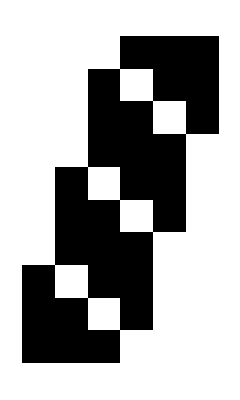

-Graphics-

```mathematica
ABToBA[init_,steps_]:=NestList[#/.{x___,0,1,y___}->{x,1,0,y}&,init,steps]
```

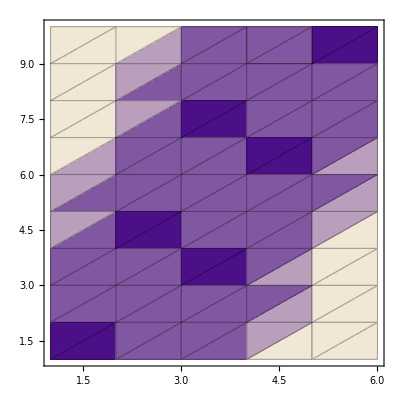

```mathematica
ListDensityPlot[ABToBA[{0,0,0,1,1,1},9],Mesh->All]
```

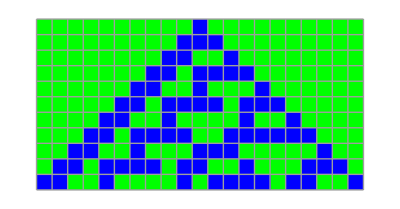

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},10],ColorRules->{0->Green,1->Blue},Mesh->True]
```

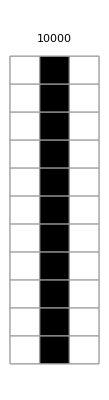
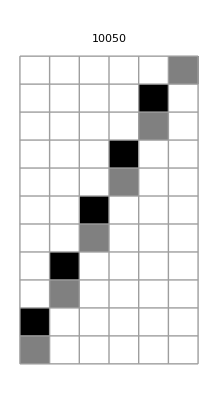
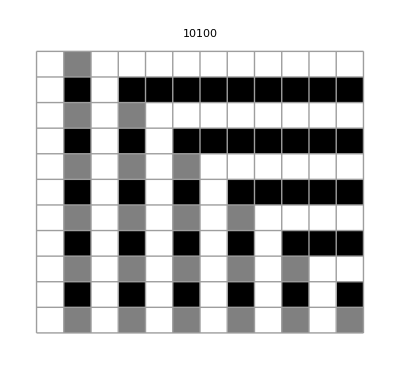

```mathematica
Table[ArrayPlot[CellularAutomaton[{n,3},{{1},0},10],Mesh->True,PlotLabel->n],{n,10000,10100,50}]
```

```mathematica
CellularAutomaton[{10050,3},{{1},0},10]
```

{{0,0,0,0,0,1},{0,0,0,0,2,0},{0,0,0,0,1,0},{0,0,0,2,0,0},{0,0,0,1,0,0},{0,0,2,0,0,0},{0,0,1,0,0,0},{0,2,0,0,0,0},{0,1,0,0,0,0},{2,0,0,0,0,0},{1,0,0,0,0,0}}

```mathematica
ABToBAA[init_,steps_]:=NestList[#/.{x___,0,1,y___}->{x,1,0,0,y}&,init,steps]

l:=ABToBAA[{0,0,0,1,1,1},9]
```

```mathematica
{{0,0,0,1,1,1},{0,0,1,0,0,1,1},{0,1,0,0,0,0,1,1},{1,0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0,0,1},{1,0,0,0,0,1,0,0,0,0,1},{1,0,0,0,1,0,0,0,0,0,0,1},{1,0,0,1,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}}

l[[2]]
Length[l]
```

{{0,0,0,1,1,1},{0,0,1,0,0,1,1},{0,1,0,0,0,0,1,1},{1,0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0,0,1},{1,0,0,0,0,1,0,0,0,0,1},{1,0,0,0,1,0,0,0,0,0,0,1},{1,0,0,1,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}}

{0,0,1,0,0,1,1}

10

```mathematica
{0,0,1,0,0,1,1}
Max@@l
```

{0,0,1,0,0,1,1}

1

```mathematica
l:=ABToBAA[{0,0,0,1,1,1},9]
```

```mathematica
PadLeft[l[[1]],15,0]

l
```

Part::partd: Part specification l ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification l is neither an integer nor a list of integers.

0⟦0,0,0,0,0,0,0,0,0,0,0,0,l,1⟧

l

```mathematica
ABToBAA
```

ABToBAA

```mathematica
ABToBAA[init_,steps_]:=NestList[#/.{x___,0,1,y___}->{x,1,0,0,y}&,init,steps]
```

```mathematica
list:=ABToBAA[{0,0,0,1,1,1},9]
list
```

{{0,0,0,1,1,1},{0,0,1,0,0,1,1},{0,1,0,0,0,0,1,1},{1,0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0,0,1},{1,0,0,0,0,1,0,0,0,0,1},{1,0,0,0,1,0,0,0,0,0,0,1},{1,0,0,1,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
Map[Total,%]
```

{3,3,3,3,3,3,3,3,3,3}

```mathematica
Length[list[[3]]]
Max[Map[Length,list]]
```

8

15

```mathematica
15 + 10 /2
```

20

```mathematica
IntegerPart[(15 +10 )/2]
```

12

```mathematica
Map[Length,list]
```

```mathematica
{6,7,8,9,10,11,12,13,14,15}


Do[Print[PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0]],{i,10}]
```

{6,7,8,9,10,11,12,13,14,15}

{0,0,0,0,0,0,0,1,1,1,0,0,0,0,0}

{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}

{0,0,0,0,1,0,0,0,0,1,1,0,0,0,0}

{0,0,0,1,0,0,0,0,0,0,1,1,0,0,0}

{0,0,1,0,0,0,0,0,1,0,0,1,0,0,0}

{0,0,1,0,0,0,0,1,0,0,0,0,1,0,0}

{0,1,0,0,0,1,0,0,0,0,0,0,1,0,0}

{0,1,0,0,1,0,0,0,0,0,0,0,0,1,0}

{1,0,1,0,0,0,0,0,0,0,0,0,0,1,0}

{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
PadRight[PadLeft[list[[2]],15-IntegerPart[Length[list[[2]]]/2],0],15,0]
```

{0,0,0,0,0,0,0,1,0,0,1,1,0,0,0}

```mathematica
PadLeft[list[[2]],15+IntegerPart[Length[list[[2]]]/2],0]
```

{0,0,0,0,0,0,0,1,0,0,1,1}

```mathematica
list2
```

{0,0,0,0,0,0,0,1,1,1,0,0,0,0,0}

{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}

{0,0,0,0,1,0,0,0,0,1,1,0,0,0,0}

{0,0,0,1,0,0,0,0,0,0,1,1,0,0,0}

{0,0,1,0,0,0,0,0,1,0,0,1,0,0,0}

{0,0,1,0,0,0,0,1,0,0,0,0,1,0,0}

{0,1,0,0,0,1,0,0,0,0,0,0,1,0,0}

{0,1,0,0,1,0,0,0,0,0,0,0,0,1,0}

{1,0,1,0,0,0,0,0,0,0,0,0,0,1,0}

{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
Rasterize[list2]
```

{0,0,0,0,0,0,0,1,1,1,0,0,0,0,0}

{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}

{0,0,0,0,1,0,0,0,0,1,1,0,0,0,0}

{0,0,0,1,0,0,0,0,0,0,1,1,0,0,0}

{0,0,1,0,0,0,0,0,1,0,0,1,0,0,0}

{0,0,1,0,0,0,0,1,0,0,0,0,1,0,0}

{0,1,0,0,0,1,0,0,0,0,0,0,1,0,0}

{0,1,0,0,1,0,0,0,0,0,0,0,0,1,0}

{1,0,1,0,0,0,0,0,0,0,0,0,0,1,0}

{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}

-Graphics-

```mathematica
Listify[list2]
```

{0,0,0,0,0,0,0,1,1,1,0,0,0,0,0}

{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}

{0,0,0,0,1,0,0,0,0,1,1,0,0,0,0}

{0,0,0,1,0,0,0,0,0,0,1,1,0,0,0}

{0,0,1,0,0,0,0,0,1,0,0,1,0,0,0}

{0,0,1,0,0,0,0,1,0,0,0,0,1,0,0}

{0,1,0,0,0,1,0,0,0,0,0,0,1,0,0}

{0,1,0,0,1,0,0,0,0,0,0,0,0,1,0}

{1,0,1,0,0,0,0,0,0,0,0,0,0,1,0}

{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}

Listify[Null]

```mathematica
list2:={}


Do[Append[list2,PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0]],{i,10}]
```

```mathematica
list2
```

{}

```mathematica
list2:={}


Do[AppendTo[list2,PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0]],{i,10}]
```

```mathematica
list2
```

{}

```mathematica
list2:={}


Do[Append[list2,PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0]],{i,10}]
```

```mathematica
list2
```

{}

```mathematica
list2:={1}


Do[PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0],{i,10}]
```

```mathematica
list
```

{{0,0,0,1,1,1},{0,0,1,0,0,1,1},{0,1,0,0,0,0,1,1},{1,0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0,0,1},{1,0,0,0,0,1,0,0,0,0,1},{1,0,0,0,1,0,0,0,0,0,0,1},{1,0,0,1,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
Append[list[[1]],2]
```

{0,0,0,1,1,1,2}

```mathematica
list
```

{{0,0,0,1,1,1},{0,0,1,0,0,1,1},{0,1,0,0,0,0,1,1},{1,0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0,0,1},{1,0,0,0,0,1,0,0,0,0,1},{1,0,0,0,1,0,0,0,0,0,0,1},{1,0,0,1,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
list2
```

```mathematica
{1}

list//MatrixForm
```

{1}

({0,0,0,1,1,1}
{0,0,1,0,0,1,1}
{0,1,0,0,0,0,1,1}
{1,0,0,0,0,0,0,1,1}
{1,0,0,0,0,0,1,0,0,1}
{1,0,0,0,0,1,0,0,0,0,1}
{1,0,0,0,1,0,0,0,0,0,0,1}
{1,0,0,1,0,0,0,0,0,0,0,0,1}
{1,0,1,0,0,0,0,0,0,0,0,0,0,1}
{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1})

```mathematica
Do[PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0],{i,10}]



list//MatrixForm
```

({0,0,0,1,1,1}
{0,0,1,0,0,1,1}
{0,1,0,0,0,0,1,1}
{1,0,0,0,0,0,0,1,1}
{1,0,0,0,0,0,1,0,0,1}
{1,0,0,0,0,1,0,0,0,0,1}
{1,0,0,0,1,0,0,0,0,0,0,1}
{1,0,0,1,0,0,0,0,0,0,0,0,1}
{1,0,1,0,0,0,0,0,0,0,0,0,0,1}
{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1})

```mathematica
PadRight[PadLeft[list[[2]],IntegerPart[(15+Length[list[[2]]])/2],0],15,0]
```

{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}

```mathematica
list
```

{{0,0,0,1,1,1},{0,0,1,0,0,1,1},{0,1,0,0,0,0,1,1},{1,0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0,0,1},{1,0,0,0,0,1,0,0,0,0,1},{1,0,0,0,1,0,0,0,0,0,0,1},{1,0,0,1,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
PadRight[PadLeft[list[[2]],IntegerPart[(15+Length[list[[2]]])/2],0],15,0]
list
```

{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}

{{0,0,0,1,1,1},{0,0,1,0,0,1,1},{0,1,0,0,0,0,1,1},{1,0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0,0,1},{1,0,0,0,0,1,0,0,0,0,1},{1,0,0,0,1,0,0,0,0,0,0,1},{1,0,0,1,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
Do[FoldList[Append,{},
PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0]],{i,10}]
```

```mathematica
list
```

{{0,0,0,1,1,1},{0,0,1,0,0,1,1},{0,1,0,0,0,0,1,1},{1,0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0,0,1},{1,0,0,0,0,1,0,0,0,0,1},{1,0,0,0,1,0,0,0,0,0,0,1},{1,0,0,1,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
list3:={}
Do[FoldList[Append,list3,
PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0]],{i,10}]
```

```mathematica
list3
```

```mathematica
{}

list4:={}
```

{}

```mathematica
Flatten[FoldList[Append,list4,{2,3}]]
```

{2,2,3}

```mathematica
list4
```

{}

```mathematica
list4
```

{}

```mathematica
l2:=Flatten[FoldList[Append,list4,{2,3}]]
```

```mathematica
list4
```

{}

```mathematica
l2
```

{2,2,3}

```mathematica
i:=2
l3:=
PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0]]
```

```mathematica
l3
```

{{},{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,1,0,0,1,1},{0,0,0,0,0,0,1,0,0,1,1,0},{0,0,0,0,0,0,1,0,0,1,1,0,0},{0,0,0,0,0,0,1,0,0,1,1,0,0,0},{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}}

```mathematica
i:=2
l3:=
PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0]]
```

```mathematica
l3
```

{{},{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,1,0,0,1,1},{0,0,0,0,0,0,1,0,0,1,1,0},{0,0,0,0,0,0,1,0,0,1,1,0,0},{0,0,0,0,0,0,1,0,0,1,1,0,0,0},{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}}

```mathematica
Head[%]
```

List

```mathematica
list4:={}
Flatten[AppendTo[list4,PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0]]]
```

{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}

```mathematica
list4
```

```mathematica
{}

list4
```

{}

{{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}}

```mathematica
list4:={}
Flatten[AppendTo[list4,PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0]]]
```

{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}

```mathematica
list4
```

{{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0}}

```mathematica
list4:={}
Do[Flatten[AppendTo[list4,PadRight[PadLeft[list[[i]],IntegerPart[(15+Length[list[[i]]])/2],0],15,0]]],{i,10}]
```

```mathematica
list4
```

{{0,0,0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,1,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,1,1,0,0,0},{0,0,1,0,0,0,0,0,1,0,0,1,0,0,0},{0,0,1,0,0,0,0,1,0,0,0,0,1,0,0},{0,1,0,0,0,1,0,0,0,0,0,0,1,0,0},{0,1,0,0,1,0,0,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,1,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
list:=list4
```

```mathematica
list
```

{{0,0,0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,1,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,1,1,0,0,0},{0,0,1,0,0,0,0,0,1,0,0,1,0,0,0},{0,0,1,0,0,0,0,1,0,0,0,0,1,0,0},{0,1,0,0,0,1,0,0,0,0,0,0,1,0,0},{0,1,0,0,1,0,0,0,0,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,1,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
ArrayPlot[list,Mesh->All]
```

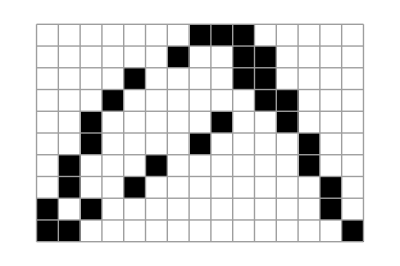
```mathematica
-Graphics-






Function[k,IntegerDigits[Range[0,2^k-1],2,k]]
```

-Graphics-

```mathematica
Function[k,IntegerDigits[Range[0,2^k-1],2,k]]
```

```mathematica
Function[k,IntegerDigits[Range[0,2^k-1],2,k]]
```

Function[k,IntegerDigits[Range[0,2^k-1],2,k]]

```mathematica
SetTest[list_]:=Block[{u,v},{FoldList[#2/.{0:> (u=v),1:> (u:=v),2:>(v=1),3:>(v:=0)}&,0,list],u}]
```

```mathematica
SetTest[list_]:=Block[{u,v},{FoldList[#2/.{0:> (u=v),1:> (u:=v),2:>(v=1),3:>(v:=0)}&,0,list],u}]
```

```mathematica
SetTest[list]
```

{{0,{v,v,v,v,v,v,v,Null,Null,Null,v,v,v,v,v},{v,v,v,v,v,v,Null,v,v,Null,Null,v,v,v,v},{v,v,v,v,Null,v,v,v,v,Null,Null,v,v,v,v},{v,v,v,Null,v,v,v,v,v,v,Null,Null,v,v,v},{v,v,Null,v,v,v,v,v,Null,v,v,Null,v,v,v},{v,v,Null,v,v,v,v,Null,v,v,v,v,Null,v,v},{v,Null,v,v,v,Null,v,v,v,v,v,v,Null,v,v},{v,Null,v,v,Null,v,v,v,v,v,v,v,v,Null,v},{Null,v,Null,v,v,v,v,v,v,v,v,v,v,Null,v},{Null,Null,v,v,v,v,v,v,v,v,v,v,v,v,Null}},v}

```mathematica
3490872398472*237628376482764
```

829530340557393764047936608

```mathematica
2387468234827364827634872364876*2376576347625376523746527345726354
```

5674000537597623462948364860238702281427379854124651615937142104

```mathematica
1236276525672765127652652176512376512765127365172635*12734173547152437125437512437152437124371543
```

15742959830187646506717912913136946977399858233814802872436855463855446674284402959540076325805

```mathematica
9^9^9
```

General::ovfl: Overflow occurred in computation.

Overflow[]

```mathematica
9^9
```

387420489

```mathematica
%^4
```

22528399544939174411840147874772641

```mathematica
%^(9/4)
```

196627050475552913618075908526912116283103450944214766927315415537966391196809

```mathematica
9^9
```

387420489

```mathematica
%^9
```

196627050475552913618075908526912116283103450944214766927315415537966391196809

```mathematica
%^9
```

439328503696464329829774782657072712058010308177126710621676697750466344744764029773301412612482563729435064854354299095570379503452515853238520182740967398746503532324400000659505126023955913142968176998364877699089666171297275956245407453033190168644894850576346492691458695174281789557994923607783461486426448617667076393901104477324982631297641034277093818692823488603426279473674368943609268871793467206677285688478458498235002859256706389043030847945506577080623430066283504397583789044245429585982964571774605868466160379567432725704121260940939343217905975847365096315872153240969882363435363449775254393010368267343970426230801390250903399147001650831878665172798468587509747439118815689

```mathematica
%^9
```

609683485452741112075235500724516670453115716895320025142055544060992206118345733195670930601391416031419347837381484188382881951433379123359313314933244210601512487020777732791222771893404859051590828696103799967120373592507057411946836370842145917500334762398351641542409564168524317143715760969367337242278252296192257755590138005663105597330353536830297965125372297102681424686850910639047766049279097023890339143848228023392943078063199836424226954041357578424782631862433423874215159238431543345109430718973560158757704908903172111956056366259712652853432607460910077283409427311989607857053110397329989034825569575562188685305447453330677591022902049353489382228107260629232409368999333685042946398487309186571606142468757152565434485212541721163897314567917523997823121395142317145049341594054811528070197536688303888476958771977502323653181348467752354680020863378480973818298508318268338696302019357148521532095273598636209307997253608343889856073384560577927572337867354822396908678510662371503925980869702639576971942702430789055678881944576812182580901378418898294860706790263994597430111831268711625556356745728755442130871232085685099470290641006222674784729223127188400448612887433108820629470380367355057572351376001828289026362967862424639273455806774138381983139391719563215770240694287203849677560831055766278286055921130338563008375210500966795010401951960267177086738862889331978106287759384737660872735552451751086042784918872934904760782042675129004924276356715421301922392188236481891996346794784316632052651079636553853158992053677395693092569827914929328904654596217077817628463493264816138623805861253498858607687798134962850649623019007141709446429416140168901951026952245323112428680444922280963531416429758022613714116143602824821189791450690561785985328865796850032627017572718356490100095105676235076142976078079397192618073886364752590488211991362605688529536772962022417040606636121435964110777395524949160680134182225915191726034865406003390625199182193704990935060676374990819823281721349606987499507449954162729524128628164389806486941191778116951061002959779309792915802011047015297567696262070807902590624341424651267523754995634828034132969009161722806818947979129519104094176659792899101273912529107352000213040998391280254936459774378680076331527294505187943205606116442740735027269981199798634681059824749208723590031392046892644888565623488228129233828270657491063132675457565165860856375112698580144903082943537288750935180048935928242409821465559574928773585712997132459879081492505228338041747218371864192537854458115384458443284811117109223158217922975271342526900454021410737004974056813740347900173639584819288397003446440395559967822443984946809649260538989890854424983749760215218502405535051899734436256808729304654943315380632199248966175218154536579536483392432757168748519548575914463080864612941543657975520976698508121839730376700637312871357040723739391173247004119377996460400136958194519944877775553905441128766167615205833101791439083812012979266215373806281902732533005665368905557306549177307201247839098755527254576243815293172818701056068187094337000830025044568191819338246332521176984917533143001303544936037217109408608296056961292104677778033512569311185669611058156875751920862714153337048248861344354574341358632587875957691369942874935898638113322640421405566881801965340015901941334817653304156100386242603374489197264858144897492256153754185247688137724095468876305401685269185649055671895403415607192750118946813187627716825769308937935281809880349065098912099942537186223480096589842500124598628855341293980918670736710752753161316977986970230893132883568092722417036577397419329711576046702965060147303177816991840555167389850793397172373291960986137884498969842721115448203731755432055446123713854720966435544053834531814962725787835476454058961787095965238820001762972262348644726507372696136062630889846947967042157274998728255423717506038369054453802699448067181700320583324203971673532509015002200198546220101578637871060271773723985735326312490897528624974678487604360480338646780392785676973708354370116343339372958090155236556264989945152110748284990609230744137588556473478169632324717488899232327650262587730415443828624213119263203235451460137506301422623063069888778412569821819038214360262079585844815271405169278081934512541484799168796365504402617926643709383546636558547065128407589965221536380360737164365161493586151373734502449275476098556849692098238927272648082451753057111398571676688567362269137195467250570594417851428872922702596328004678205243912526004349040271237573969332446648270076706518450787059045724992001802132113820388790929299888571160776522939260299171326471468686458863225497475144416893501180850829978771146935472015137175966533057924747021216126848140769146794309982329972559295289075792967956351607513991727110220921498308244980078479795482015372569623224939778650251487071756534749451100348226056933967588391354541511849177686493559219699542125182527593907861122968626554629883926773846771539543101525574189543625600541697540076702940379874888947144612158982466646309842628547319739077865331476463453992805226514211097711176423255674183845477168040599465258972388573208431575083860615979810029275638989851003295044555549243113839462378873502369543130242015660020602787973598572467060957381241565941205456698910482067836113482102280524406646302743470112087427472514013105288633611502785188213067980467300746437302992567150102075686265552843685417392129983164451911558907471068830798391649115996205050608599640736308585851400373853700540360971706698324794296838560001790320259128642537657946233749749278942121508917513079964037379047390153778173542741898479242726687382246938596706657693174111627846656799557424571601651943183512955281868385914251451010073404817059514241233091408860258393083571386081348796186188323378867994721747659028673328480484459679631662895194137215637219320119109291791279254127828570290501391758311749047110360962043813923111344884366144770117586736537392472191116611664818657084338613647063339077288169097994438000017977949919329083260526096133403745058519219706445278520075152513671209817461154580997332471621813987611514972532379635692724472346821600549802125671248433668213379459545260244454772731023174256697609

```mathematica
%^9
```

11639648961714476450037112738383513701181195287418707080477275981232671129306111037903049760060898121238296130301019497278726966272049388713194128225979023308129092419674085697726125127231888109702493278853489579795408897939203277384285773679535961661261068318224015244212929851142581276122359721147732525778322807185432006841500874332599997098613753825177560964766837277637864923857683922648792517375288191080725768660644183809995247401681316777593378494209891918912461911687181082653962213116813336289932543727809163980517142643200155438323771793428129320093391802215165044168016934515921205741263230561050257723474388653062447934015928091482650554984810275277724993007139411597570698864367151614307459425911074244222861639297031502438339653294393771720151128938346167994349146563270530661971474188772479109170232137756371665828845176504806408429212322075171273540878327877190572230292306210570480073028554859411461285581024116892411551329679950128398971475416464066712422319248195174532206028872702191704916495599836385879719879574031683509138988449747211206152179098114477455332289461984863166935140936584395821022980455837524627490545660815917559283310540514767174465156866999849023553599900220724962782445764101657604021437175796597569554186221816303942379151381005297905821734552649346487356043813997371183117457745364785244972136803902160618302869528011554553414922989953203722036092292306044470865125724018823854660220045597260538272615372381556637844838295450448366912153569301218474459976541085743317117656796218554329791329813614236110102962504388129113792933839352295141617588255675362777922438476944296183868577287895787182205475601198236748785534004047922484205995545205477152480097148406440747906100856766258080890068672162062655802215660383730643442483681098614726534378014375128747284642445246985650641401149317694606119237288616405667763565613309211818501130103342630218844645426720914302537690411841187938670413672616612915491541208723033852853890633057457224226425376042801701024900141323283819620300768640978567747755292225470068219241062270443261132742143965109407030776294974878389175281662969102088819028566452861826875437105798722027400065387169291977147495056663808555886351593155503617152717162791135011067951094336147074064088450978446812018159902160652793179429292452425312406424514827658872966033953963693498170639927864624002102360917971895193743934433245410762665650421039161519267971555122964368309156823709067933211249132694695154832237634051985937533208447666646104946506256169758347430451620212056259322522985800300746968062938233977081382324177223896010463382572537554981135359790592073778200420670371756379004945225992294587850880616564182647862566018824374040522659686800421828011490462800570916156588525218567147579006802608882868146322997489641265945249313372219346484692603687556723844798626309975040744913441178066529047545303429640190035521034001664574284378925803256837826516473329796262604494410039997670784091907329059768030216078821697328625911974195549133441807557111667064341955860471340728330183435892584857133019821272767882951937985933551489408247302551931045573730928056795002442034538440621295032895683464169066369848206946597488141611279629208637343891194837849270610666074020186871625599636175130457564803589503177049403509589339913313240684701109537195554686384360245554269823628170079484270850113327886841333103915837068095801444696868827019093538893955033030337400861396029473285616940772121383749006261779144450858917486609650370394215293352881141152234518184346655274804363181857862646520487294846375056217020758443639288097022725323528798238779001816616241118465249524371428064277073975096816371583091808736765252609799798634404773845065992576941118282602047533533045762707276222224464828375651953150858157170235733182401957993826226441011367089204765773287880565800407416667948858727084751836761382942666241142361005349707790122090775445878037023443400993677467632438583108966481584166001603688646892023928152501868552008737550999023575001223775505988336414866115858728123986657269320789988012358694917932666845837529670117405547021159495280756206941673012473117319400626877736465084585279092759827995575902549044969842402341445718100742816892087837446729144876669385783667484860027485156730958367121053440359608472791334789549285335017383970907119243589713246256462057038272722752425938485368735900596972310828437945866769633533527815039020859418709766966035773557679112277121591397862083985781163628097093703418647433965787934057447583719579715151745430884842607668338312488854753240255920755844793943430232497400780644721429636519345696998784755734309309510733288342925689251647860686044437885615788851298706655568316626631554974593150826007051929692363084890286550261691662492587885433035759234808683513580884221750059426841277915693377606832061832007792045226358410442686163539905659074798556780467575524664988857213420652486269650027938368106621736653584536152123804623677127499128366756748172203623151080730986010122046443484582047215729472778597401410395902912368030856535550612174958473634362013303892147186135676746145859617574457292765370786839288919721781114423463253550120293527933569549877263266173670188833902881106346879603406954428823517722805420380399916154058971388518442921540732722287408934844050606515804375139580246017579593545052248993012416590775562359613443465700839571151714829863589456783702852454027716027846232099502489979647604914325431949885518699453027333048614717848818794177778628700090584422396515759499103680410357743154919182319966075162791233871940665127044039315367913063213382081575248158432226856857288783177562121158598808639429526128490540430854011453443687355027483922695198391007227015001443802506144792905472263818397997962706612456731604339266092001957506306429827189061558781072682983907807279610493462917308529044859286773947393469673833395060694752002583688180989319580521625667555243982262288223642483886432163079388434656340418062064390731811517522818834349734407714526440077335193881284751354434410256582656640058217399452609592366398057163657591002446962784523785976158407345838604333452061274793884844427780785291478481771021686533858658017809924204176085531002030797885784148962074463939869442090785071081714354786989130067972558127313647158776795617155803612276659332767878142901256679788752694622194217733180791355537787850925812577166974159221740400318069985936861079199970981955125116656185947043399729702619405257425696948110892350460840637671445416988890433582350200786491698922469597256332042548399456768471780167862475113891420582008071516622964238501632929762692715814131975885286337129927689482365264270683635096714945024213744762388166238681781120382716159391848431364614169852369942345997827103406856866711061878952071588450948068159391627757262450974862563021287750060041670234928517638999574705405249420154279047497837432598824250846413509431004809033336149296459413329279539438647109454942427108518162589139658144088114009927596141920733249506970138678488825699080393027014006482909399332200927140314848109534680353666104708437573700954885055170337065685956373196155406993520460687554627251457446217792278687323633290274737131304707998010156894761339862775019276504541217133500965680298284952179183004119734959445320373993588743006289241057689111174349867397236247585679054636362004776691646293995163037121337675839793842890682528878800071627190478278177111028658987594883496180086324882007634305882778015260336617108920119883091007062522214503002489537031984560411569867192481584494055654790769886769728018119206082733002430830813196216993958710866625219974375987983649330006460307659249900339585582860067797718449187036440986929717054475878185911572370533563480158933324465914157611642433856975086980404415657792653320317762905660590270250331790590496532888172785760933645522467474822032131840916466271160625639289766426201735822678261002750274005829047704279236854129837188698424518505763452697334405498673048305874330997995849318879963489630356904037612278435334836934718449621884453059243101299546143976492120450924858403137165424911517732855346646783949221230795838962908074947898914598554670838407500986604992398364397312757199043071056067548180570090222978726266525663848809002672376685172220432152058747055261856968856913662964654377100070283175497492763636458211787829886092036443822463493943719665183633873146667534291912317248034943745644196994159382640541201334670301522563494094564440885067206420030114088247836904143054703184342586604165452107179687550194811837809675363930885305074628205606446512677084189659745739332097427099724351620172021220212403067874616335895267684593513910316133326795321200156134695374319518056536402144225395534649918109492587138915755718986305850419182285039092574400758659804468585257434408645166879414432958304911393227882461529498524342461331190234120928165548482158411326791734770357258375655642461920588600605389274546215576305043568892884848099448494899069389273306481941718222531237498219717713730903486204330098808940163247817479555014725849583173557114126926750419747862426838423204727658321861418434372928739860153650527301391635975734481084718431753328992866311846255816482302563413066531793775565338808930049713950551549078707264411854563703051099507553806696496361193667781746134983298076746057951676387866824843581808336795926483525024903509867433868243484397579591519762079461833363557814597314393035569967536807697619047737305687790506775747795930815385617795167337993251848810573602326967439501199789141960590239574553872159085718551529145135192109764565468158545197312914401233644695707212148585745852766641284170726494225098942340772473391622770563461000516853467865387966988129251029515646457639376592024857857897829492208538026975975436188202012412326173066505233815859004728410858364814008168299752843176262042337246715934841591653026800772529339989745550488505487278167338554501504794854532781999010006211470555868097172846192025072472749876654345472543525943797979994315742455697866609720970162852860261283558878127311960063540770562351269087242622813669328046624002478637858743944362804206100940386602690072767528181938260238180798192630461526911976056513455791701777058046046327448662799526625354890265050969567755396390218880865094718043188990453769143207863633265020149202867977713062862208771928591906493912735749653732105813065481707725169674422302037078964557656302491557413747762862609935127698000874123937429830545689056348545386066119172439404930226384616918180973107691096364526179171831080804499452735057197240950669556173136941375783746982587938547033674629660855628409452564589394547122932483464587006198481862150676696585427364067768981839412194937328648852447923154433122552243239477304018048444099214099793614978415202745987704321895766818421689205312909820624048142993209251674730960693614403391257902746508420443535911985429004059874498832965446288405862864914501669805842039187059566101582821619668307922334384809219970111343246986314091798954548207449015977283832410253476671307104242714687595669813445392797317763105050891247643364604550190153261521497270959287986997705285543172821490727601564614158139969996127697967505705220690862069031183023235179730551365398082123762946816107179430635297631153763723423780026712523918434364045284392970501892396358412608683071887803235139052511493312025146517452862676462396242589566205393214477240770807837340293459247703906588168247691005866468219960240372651463482549539047500494054887460518527028658087520664232539665400681652691785181737114856551083220982364591451727406564133295713271378237989727656357497986106336961633005396676568668000422698536558963566767818022773486755445574938205985642549114637003111363413226960828274580694596393399288115113402267939311681764871761512782181991856908893244855012731882007737184797208350696537099563874696642585489759929505884727238983086063100286135204503300634459091323045313347750038089096569019126486170313827058603376172134739123627766745491778830658353569990348673781504195242939161033387803884136103460611628182879912201587310612007499578001589843491053069943296028054371001605455760247635669633886054196196265809763278997853996977072310256182845361972737625810074805994847371293549048162386709516915275159772229459815281292525208370837967153807465343991391603319555942408169878539065644554234778503698993106520154933174739314496335208602243147578854358411212226355078323682852092968888312091102855934826549899494786902748328259189207011041686969414490667320838831190947745706115450687585968141618182081747019170241419582836501515957052409455257959027865961803280426562515844435576463197210281511033227428309221850587000358784197980624921477911612055767900808876488562867060713462732775933240926436882221713733059053309693281363922820835156162596285108763893258114120445645134765008310366630520789066276002463250102912624344297693046461318405595005979602253472978806731580987677599273945467825670672637756395957813055305027079626879979267063530892831491721835147284721303021600831998596648500036318777350283506062332858324780032443645835987775255770210113816070790453152808534530599582169407365913558363739802737675216078031228093771990066091157420540588551382618425394897980473347108812329935719888916757032101537648826811373209656807053660818854952803662351923207921940303680374237673671395441727580077551371339467959464839355411563206182899642815883293150116306825495493454591656664755837910751411689042059528259088287978728805819622975388968118872641222642210236120814882756256078041063103962505318608594002399279026634509154963861059793431118877775186528801118920350610975487824337249169605324721148892904254851186473738718856134017696789130817073208114538658810679713597874550563179943537827510339822665855316300900875910034952181162349484445453445011153524008348443128106281462743849450593063964615497884069590116486055634644929619221882605707523696426494835327341353287050380499778588243890475145521413538298638629411591567716948177914260204665297149529352208104808704063260541836968163968723131218306974067860826373729301545995743092251647501515168590588867562182203991739732800764432417221021856345738739785107380473166817262719855340476984866823385698009091068431326147746737723978459239733393916781737763707066633459459032783878145045948272713191718816953566231471038218040414220495045125653818652786946373313186515273620193789425184151184438998354510659092995023846625304975361837772439279583808015269332308097476798708460594661745514372105985841018250833187601701925122984705086033221034982227912599409010290830175554484089933832011811219307216614185329213955395135333878811027697963315254536220035970517466564637906829533662326331205215496616561530119973906968070277361243270635484688372626913789085625432184316301840408077667948911432149605540006949074360476689393330593108476008043181857565464141898404288525633799193695024401816567634916132561127823168753145697321616761129840419072449846680858493522518366575227855519160782757642675999275929445476887657544807102730264306611745728527281310652981080085572571237603921184407183458185215079834720382971417414764992644879341922264127610114281389913050163637301088530370236278875946656506195804844282204456784131953560144238615313776080359085434748427403484188861848500353255899115928272458190548147972419513128599565867768071136745880327162239043908300187794295548084875970097283984916424321302090794810422906545101445358230948082319260630539152481830756363309278410765916193360143002101674676100879108785817888412829959716460429103205215262309262840746082115111573574129951408089872094302187792158420300630640408962073528350755033234682886936458374680049464140805484679467379145316284738349184317209133716694416197331605880578047461318607366093514611390323180633981002745773290010080796484009002613812372148814677734076856694341122082228287815021617047080481287455009469523674373901605980553048047169010302573267114450021310841694404215157547376709171295189068852866991510229961391257059168628808909766378194197484847010220742473530005691843084219610037743019225871518441460923613468912329715780705866793329731164855243192191019791666651900432585634395621320845758125365662327147468640253781929633045495501473078495295110204257555407857968137653444743010336825054146434686902353372322499738823958567682877372045549395858441309436421779351789620521006666211776752103179940959837586037608116905449427083257070872098201237861321379381883921357678848787795567940185806975112591644368505265532588582586951948342634339372258276645622335462158762527779520317198852109681645464657975202824990285969360729439549015156133915328623413012204843711385790842407771591984256972755518604593901170679962409334568877111464121053281528024823777552325693028435615442340488034936937942601846702094174337314527156169628376713436876047550761979195601804539860261749342372225174005639515604599689232672597389399441316565410236667175153165747527107956514213741565054974810042031259766482982197998356326108814762631923032940645669832771052764828840942171395294037740533931123427571749582969475146077858071634684035512906675782051786710699660471993410145391450364623504781060745823168530040019007302107935614254482058957318135610853491903226018798347265542409055935318426975838328990044018082781279765562256676232253054527399867246045237405156713260593548349908980303909281425926486598866443803362524362745143373293470102414567396735362137714930190955099809619477516670198264747087897030212530465342293631301053787994269863482658392792127872120129247157067481223874780156310051772441529552048294881462042516508481745650476233549910550522769655612674158392644248916645083103011267726314567396930846506708495571257174559787493725507171637115446245771600060250993189930798949395355805605075361954474697582533943621600540465304804300028596610153938782782174165223878723238443802602025585285076715418784503091368995044661784632845421070169752967498525222599243687578678180316397415136477653331613444663409630680390718604975480840537850949927520548440279876877496142356654458805328841035968959213179169080463507331533772686470924437612240743604202963000967576277499503544207720237074949822129115546740203929318066515340637253970242687326645364586226230087616576426027868871723647649846164446067519360442789464361630344871796991327974745358156021098637364079129068563757952866973519600476031279914888407581732765717532880332107761946014897069229657621493742154945246220410886326124611275171521187742335167182536151425269511008541811149919864974498874791397323082743984663286669171802765152091783343324904150012086957212704502337145565496549858654835484148299819503802272809537054945467629646186989436092943360463235116765310159757708337086691941051735786988401280618863982751029550620497958599336226516536554350298584041867787669231473380440247368002179102217376666120221958901486612576660573858368554287706196186472003631376499074998407798991106488020670678391611225226818282216847090012826297911637454044669989177762219691494092883869601225259781004550555076884384213934583199175367350595675157549154717883033972994270707933855725352125028485588099524895348779496981067230140850116691893636342670163188250877291464007534177419387556453153610844705404759144862101252954106663418769073433375785843279982264419492149634581497327192171662017839712119292111847348349248568451139415149991436206860588511552426703014789838315130502070486943663543284643483804385240219224586177676830769603587215097325184819985954657182046637937933860756644947956998913314591548844460342054989251948438475150455830869900731909820770832520746155256546493248571763977204677501330618173386846504643229432651997149823760418116515955292383863608061843997926225511043150324297630575131356860924851593818351736689508508910598515946786411529286801229887964555171041562887589167037542910286156705475285205426325157107837098032513640170894306719852508389398978923032627117924928240661982990247559532568825769559015181201110131164524491292187452315918347765633703236476693808351246998273879677066716995391999294264235413039979340512959001856586931024737070812321253868521208602137700857625776058667654699907154534106568426763865126538417154168133662715987748998866058812633028986796062375265861133685206532027311079159384218583798871496166816048830057252526346420835176570764688608259038632235948420981447177560876925847473145663620403141897587999745320805198685076549472997870210703664443114412853098130260790106817193132644817809853233156137362855823141264663966076191769112906887967790588431458086857102749690920937615972555876938978769892714642179949261410089989795485145520725967573762899397297695812005343142630888890065767382858387949993055546319997797105337427073405516750854079351063256064969767435849521077825983966985929718731771128554536100137761982804310634572353726542263594154411435763425625969897087250339533576634602557535221383545544162991961169705863173382579294950462345672595721024790455508647220843810182694878891592043705548004333978257889467677917557027803952030713554777757151502389164366295794313281133664742078179497383247812077510913178534929845647007376241018267801335873581456088730940036606577034189982297330820764406143332750805860447919536671247669946253740068435979109530437422722526609512814997544787944696557005667160815655243179087056430714075342009748539604069686384907698770979906823952698002740486059824018625908908412838597197683400617051324262602534638080333559823125542276336701169792463897205994591954371815809709186469807456700841208309209695753949529995207734569329751890678875536576056536998693441403067008392216108608338940335415516306732567816592387206554443376384353221526228463661581619017031110713037377294065308528218052426682197023859674277042266511557248617688593118642998479977858276159385178339687253370690277264771111360435931143365527257751103208209369087252542122864327723678512431576972153724302882298771054152759770245526787246040406826132114753479317283157287020736217696060730130541440872341918246115826694238935099858353000833014707024362662630545494771718222303637163796593747620463009039601293894126420362147897896147820970474639095702016354841879861712595973739332463280295571134305069019569729716655902256183296344023909657471725566620599241785724120698168504488226613803290612178373657903245738244962029959307023680951479838950237267332774125342561336172281835924109390788731740186986608954581042733798354467489884704049118299204849445344246484833702154064001653789704447489232657237036634185280404672359564197397568635498341706269581090534794625055595164712310539836020084895430092965048878525748080379324281853917116271313787140433822795839085442135695138245166856925072332676776783673384710057644138504138663210168718983999072447576253710671774398569572390758250789556175179118083833460544993627403678810355562542534232001225182358652799429074707704432471367023435090811864580018563162950642003255579598154926409108545491281023812722517305547084108044119165033282919028013330493333471315502086167765128215112768970350829337629222308696547465210191084419695917437506024797459061317295029824983889781216541283897501034231387201644490402078916684893002362537671477401806804660819138572709152037583240095256243599138176156285821108337690285608697448645875833768474405780919555496922840386426443795448841313334930338081425022416016133511930305244780096691535782743945496342647833784394374314076789613958315306407830903618534951754829278765837193136687090086719262789978613683777431987450911513086378426331040344397978008182084344653174186168876656239265274673125395444807472389634118980336409830192512648347170254613364512181774044887994159741917167268292473411880063152286339107970276812694361026337355721884426547658106918800944122880656258434147196260335180186556629550548661253002315054848012154575276496809308588341288173565442084353198434758323070974605800871241251847360359489394803921280976380720592113202895128201257787661120915729545500936183810006497281506064716578748147438265623531845148525537333539476719007884409872852431394504771168448868548952410470339474355535297222742789096079696035201210196245703336556103288658431207340830161879735189517722297416353605144145895485049415808191707967940857898663877019100245898626392121009532032772737997047684245296132279884256936023157761107404988338592937292964530533897052232881911528980000196974041693023389826067080091190756640122017357134107346919555324199024758441604651512678382065586451085126133116085117578398135857666144321042443560660679729519329112740260702622356285649833394381703330851745311766999215188132095068294926602715642491550066811207921162092719845926053544268820605043735497359155393164726932091030483370830478799324947457017657641060255502866939248511640786042707041717025369800884561426399941994904959377243368217382267469684216339145675980585247302453060167162338560018422840200889023539747967106167923086008314883020787196289976920576285011268335898580679457195921576054024706340011158677474018210445562521019254201650719893025390205425733546326142028967701241982673715788417994723971769009704902281022246975840663906439770241223063495538140131754089413238559113565747314316944921463390967395918472488212890528864502083124285209698670145717116055532184759448378020719872300005056198365591887964856491131683595146598422439178313470307638735503921405491272387042924357754494376470690079992434211051703000308118823990878076377335441289175797540492071556362255705254713030773139853889326988017088318009256573519424311182906617306397452279069326015347262780783811816632425230669938010797728020129410603357353267878744200331438690918278146924107699112264137593152923981316645043895885029861824948680252170438129706294631127872442424225773686897324310979343407456726809174941890235213745736677172152585318158372076189674428644533205552554312743746060670297012334784034245288582398022544246058355787128554409492408920583732667094720500577861961987897937999783927766026004104161583695166353538219447323494809795573419597730888412716127419120179792224885401819823192388603945379083049682575891240886132653985394632206569708018785124091883527071725241801742249717572903236568771555832867101797028186944651297311599587614993513978658902175712343275110463868303566350545328643899143372815825606552080944795808497024520314279497230555235215153230090705572490388548836580988579267607417242980765439206346541452576856542123599578445688348509959712265543194790134410091117405428753364724443124724051436290710331071492812661381419438010242189870946376239790552676556476755731848268935408803055680325605306521649581940710126497842808424784143122007260868006594834173512094246291507382775915093867691947180628186624391110580095359833661895068994470319263499913132254139451076395006711040433860623898232950511532476129373283500836643135745434280921797630202904723985809583018532937521361984154433894955990793725485994085937714837967602912042483654080042025158145398958516934230363213816641474988270805801331450373430077895833582077494135986663942441258092163815261748190019964844777454660651324629963535070106279577220286125832053280703921650915752603472602675022790102010141503663362581972086486574516242149294339583819185540686913568422012393962122676807578071493973954346125023747798778547726725639750889238440263028058480888049398301527865596254643173389748827156660610244445331814422226533902947767256645916421805379677885791561102161465811163211780938270545572459364455368205130272231839500774164858179915644212142115404021115479233986393090055762326548190057024557451725453554258212208582301092154007815080136555266187546400714450817863893828946325390141888953513420968540545530497942553966980966214754232121043939500476823109813636728930329309552179222949635365237482882921725317922890207816784851052799478765955634876366553074376465254357782677718529887166427685258984412745760817020079871927040166557828308935646495004851518807320210809134232293748295683166317732133951572192638679611076763193512219632054016769408565100313891396443376951878225941525695547730192407946281548251201984458554588771654041620908593760370168848022844761080271250086486197370037167881545975138218893450961027775705217659698028318545830368613523461894715033723805566583663594610838351151762911332272805742978553231036758039951720469110824446741138063685642514134750383924922299262894261685952402900886881499593851121687898834343181878896057008723004795168895956227206306948215753451199760500432955924697443697417961158232475438221489654065972649408115828971141158876342451105876457352396323260072266278600931253045507883072100071900353157341432572161437384871017812653052474158022490940693575471331745272564906178830873366811689758046152482343469154435996388645589308571945556510560828419451197168829723310819963943432889146390585701343317628180499537362663728383355776938721237398040996074375332481577207922645053513331290797237286585050360853497408621019185579635340664828836005508963702538208892099132916922368410139042667256197060878465426948751740608058484951056908285395119494696382501544135417104759044080952278579700208312042248397818617878735748845348939021273487906319464820910426353021531288986800674858361770264475518676125069981118076808859434664271848922398384606206922271652174622778043641136526379455773860303542437485255649312662019139164826742277543541166489323899795766192657497505466917584410251433885565878446256987959502227707515087802544411197178007424998734504261651968746974866254762677988981094209605399088961376415335363228502470957617635257720989240868932060923786287598067820633588889354978103853769614233984653419554130833307623124707049597879842589755365693511617390760342492298442153753020702515050125626233802113029778748283045672239390731799195850179103112261229062249459296846385674866839867326761685175098221347826365975779657791618877486179176128080306812637453626859393002858225739745288673739363857365549099998480192498442334512058486663080311206503080828220642934678861119015834729573525955349585156792103668537241914501760982105923465448554545473411702100039560120073190674546636984263881304619418019430151818401589490856756366064311456510534505714368876961225193981391165440195049612463457224463473959490735054137807884173776106868113301917845852143121524161371646857163447518643871795184191943706942839974466076891707863388665778622984111018530610719432888215900244196543705321934912304408970827124668758797758836772942928163037040080730049505952397773877260430317749259291788437876604893912627914635149998962589437809628825938235850964671885291272325412249052150090203923108422443646730068837720566777119265639374042494983958940728182558590790615667293706152639897569988401261744461180497783190533039069569460789485285843678418524698566212539591546248902538418712660429461874826717409693343611481189818282834038459843409225024934520133957704764052557881831819050345416511750964869622812724817768416866600234647937882132745606159275394170680848683520859103192338895296649236292218142928621149715561234066260846872266517535617617809559994483100938214018940536068518049687317483697318223916739152628177996381592968166188295084623055232728687954735310530744810197885261229467564057978970955928169789138880440016342205386969471665121841049695765893234392370074917487399013877392727712946648300224361691937080803139641188677586864828965627539785663516334509342018176269899050261363272331051134266697321885280145918298645007135401512912440397485316338205488243900790465247670493394362278315988231818200265459027517283939429643369080148497380244067134737796204069243397112489663694496116073960944012102603276655067073769169321375957635555038678744581415686580143146793486531720478735046555606205640941193419143283055946077015368204281750862113316052599248093957482323621721829993227736534139170271738399024458320604068429090996280771787365404958089244741936581699110718871838653871574606110559746095601560849013545780397973041086203425027338476317112007965708354758167601611883011219047672019732784087757951195699774855679431192957792860456894953459111252855221829272044935536493516597965343359797118179199298920582885047703517584195104687415125394277141607166594951036950111669983063150653545076821824895289138128198314124574359755537136223677499188002180485868357195471464992746733183627356915896814566282716937476009144274858220592266720959951210173773724965004482649688572426139261799749353676648644052153169646479684020927201025785319857142538869591724041945744853112265908869039186484750175438361472778728603259319227269884827739564975078004088396900297104447913120590684092566837647284358429801925010146738615727372230370721628272579042628997031486702568717994919206235008099023434387415353691364788865629327192252979572199944385837453281582491637644921613261812221912564879967723335467105933217197229982813243078096941134284715801091097035002456099411216253154814904757288353849613463118628831088859475840634559563392141081059559270666839782323452250957211717161766386031797881470806258522835470091778790617304994434939059566967046177266561016407871086343844324875227196198827417568245648572847826963536806582990599919047895747637306607702953351316560520753779606991670174687565113119441962197082775266310905530682539243019002788195345730879499211847007135871040493656341518125606114054308794932452089918780594866241027191452654971278982014012991106095533288011464574497854408427374866985929783289749252084293039993339747603076078043718514560715440221377101055363344075604636561073215596427492885935498146577330173633505461095518067853511889395743151420128036962884760736910756856969189057291736553340833730359547822601713393264736618835289150038931696191413540664000391907797367118780782767125013505091374296276504191891903178871323058873387803302485099250054162445838057816310645246613229798178156925333114554711091644401160533793407613671880217071585212720634869071279070213187977056390883421374166689871737504536503480608536430802878616450100133660724727467069177396914742937166484170622129351326841928872295195904802130550047404237374166113343224956182837601733084818897112483752843875990898531237324958138299299545026476021199184651170864419111483389561689518091425442486320003177316199201341011773338796048168888324417675325166406307489147679780960932293798960189025119666783360965252287651602835768572447429795286786174236978100975800144990309821002187304829498643531528951364239264691924391146977180127430802032553500332667856887909778866938775422153772098128998760444672465867831563082528710975536670457703688681188505276054799903641454602480170819630231131081479516618045752330826814307902265922748652290810142554733555350159693224783163074221696896732830178102604668333787233499264870662346667512357857648137795168317327572052785209681294501728359103315179674992602161774431127400224075395777272171668783775006059636534345462155179159534302424666183284496586955258173266339568427845892193021322098359695839799039480270716913975459369701347326487123444524871167944948741871761349974997723730085936106355788611485375112745703342890582472125634002876918225068408449226508097471242071519923087388343323521579194467531795271764714065443125925845726697014159099527417166104858505422850240625212720167166290744077764047291863036648904299449904904356636205850901515175622166072267405387933316152141304646731900525547714593313420158503580204780530865377456796098482662800293878051708612075222764460811820079748143439474522728850325613740250078274523994772421995265850117991952539205290329396497461935090245204445636859342099207088080565572083763675917926124994497729320831922922575001561651791995804517696104516181980739216472627853201713846235533249829227739936007608685522336241255130820369088529891354971186097464209946632826603135680992767512384927363289911439794277223267685856482439362707249985234790429881412511816445675914824417521605787004631560461714582026909139914264129298790246362959572763588235176594104074017198842365481486885587711353252998824731466777399778993102229242264619608260734814488561845644546190524546567070719389089942698139513372823144534937204429310924811545714020005233248348144269743607236208410114840834315875539857822455458946309460534485606125022804182944895050269900161799461149665742026559868041910060150088357278136358004774327455971428777387371983124808108704317536432538624986919451592773524498915795818836636588247354588683212465786889011443757265805596387723103683488503469745400281080787628471155693443155707337942836129885087153538372558871649195593838298768206762867854362419338824293857692792201752267757686146509427777134793431266272948651400142522842630218555967548194651182739153859276150352078643898781181975271218594215367522946203805124974052155657560825720180108723637839839019654182246093302054038160565190094345531637875200994736102212221735903837243508166287004561982595561408081127108269201607590275614390443267054571133564421851305903282690179583827766283341057525723294622287597734449364011435193918099654028370099732439249026506068794520837404499651409433703115768653087066133822663877993483345144423546588026789595315653029175373058534022542050168396750602842965339805210090763703475542963520892246085037950043807103527478427899674437715282971831616945316509836517700777505450343415284315858820652969696337863317470688393640322639757838874528157585122086585600156331341704899370239373894776563968391458362179677710887873500833437369969285768765852810210507037022535056341310303081518441212144291856310275274348398299245575136998649730170921991996947804433781279619061858268660050660931483570833190491761498186673428205465485872214261082450797483575646694531154620714230268947716569236893771301681656481135404767771267685737445021198394572083337109633534392862113024851072969124144935787917271964470350507422818613736063499544952472744875505564158049290624663795273320482492684562139711405075058155876027669266980652437481683390498943255584751078421763925429892856025046124458580092943845657150142431095659301326216327951036208989201136761915746285296464148005623012291354538880678063841900193014636234714310836479882885760633451174268405792503275179250358926258002007424652335494635740544861955075731936769275769248046915885211809049366981552359411117400973870533251158465321629826505149027890721178417096474633110085676472818209934451052042272106539023698149894864637879575354528074728471621371452592366065336540871537416327782074715857245039184345335607106776313258069275080871945136846458821899727516712671581605220066835063393745249783735729112323038479740027836231366325811602378887112698535626880130836058384814582195921712218816398409779040152144822897960337925451561605657286154339200925704586443011709021748787431591465069846209721899661155595803245331330435515107376716432402702171220531302457236097040599588938257159081570504150053638912857540075785419400881100088682560639891925587976793940529976105986669062383188964136809074339588021970663549217971201503734447092563157997141506846539385887374006201781428263004433453475060595744092672157722730966739701625198596577201610209583686677236243935011500447405034024987096666237220957964633225604716039210808901846029046724174450059833684796196744052449034121481398055709056020537602310447818549768100675932520930448220444774561622017155931561087949354706674186945595818246880786700289278978653927977888117720017480391096328453690908452233673901407098109115261643983114757718282807964068872288425350774289574855991848160783380722133256016422927667655073049488233025815595963123546802286052261194041566008936158744565739704607132246408255081008907763998413392719938842057795199448116980338511812646818144204063368801317768560448503278043958383067546884849083969011433807277729757286115253796950434892950700050168363444594384719843842868910044674125143849219651889350853685371154029427237658943656168132392726429376990164211596045710920882396377918617603008723602984771282502928271702919118638674105696475718937255606665736163880274005247161005859816730383246270182951546590186766187275489237605944431349144200490618751284122384316814301651368211204970584672263329655995150700525078879652315665509670973620108399592075940876493160827760019918609395449984933326233041945148977015912660594005433829235766240851708683353719633250171237016932137204617120716758789489359300449699655741268360906332937563732146698418441154163549331289662662795134909317649003734383893894564705563752424933231254451448053804372451868397286532690628186833219603644506971418388683445313723643117165423710804008324332865046462995309106023476855440769116084055759989564677658932615850288862695093946950841707745546807651877190350743560401503020473017491675685146720675880110772772947769897151282869782881379750951173148776229126367220307040376443714471263972217383052621634362354438678909204545379929239054466706135373162339686183651457922795758199366425762915533089090122941836059424219554377217075263264850656666355493531422343781796271421124627419355505135195502100798470240594101217642633232388109370666115008831653713669857128828081290603415970431664181903694115903424578439303243691143127397153442104697203474353578259236718745470374037744434526813994231149639736366238397851880463630395237555151622647666632580685534887475861080891726519632674341253453743958032195233681627325170311760435004690463369435402750790112255381085004515779205620886382384153785314144815014490841220430333870416074397076627319288361233233094985563226979876348768572118172187296881095559932124380962659054910224543093481633478444877302639051182821754482409515605250260722476039039620877230432412952854375769449161043577322596297183580191841655080567182693379528988105854941737216169399810588765443496296461192856418646015728116065155576724141456267036267642567486538142656281245315165015252783492602363025442359336281742202092471412146372260757937038868462082678045390882564505667286129963482907121451340008887193959475603528160302723930380587715757538421806981535928401286838201638664831824549544465529145605180831855941726841247214134992193606912515563593094758465888493340543241053623346067663801262929333694602870097664662206443088610558798732909203363101912907336786625259136599504587607817486618197999801582668621564733368067315632904744288026604791880542618101831025584481935245244804715000106373825951139818409671505525698391233769005858053776417011133758272170974415585263260873864160471182066486454884268392046666658608426281497742527993326964597561441895664195144128053033580176230716459174688101491997088427875636907415450642449676350997314024440805016491211564762509059662031177621791080067506362511370067509711289890601670380639605389270950406310448341807537170772718531893262260389375213267290117261255065335430821744226349264936184183909612171314583099186474817043639140117937486272152486153233546194225964965991518760701364775515307598808747078274120269282373971994584213160077106837488946308870906241606998891984664321716488785903194622182920505012217490947169589849199240880744100774280662380256952689654659344134628241604377376766816631279840061507505479553858634220363737545544569774078316556710402967164996211799564128034447336737453057900602885336436613540997986979984824254792472376370319536791281509502247057772300158595675445441866378307541306830908258017430192931045177584379752399567428282132129911824469219604314222482382328701888854750909827798156238781822997138798197792014272176473305987384387538624238166409729426622060547059913961149702490402930166478657825096696210831354366743492949727510330293301435818051838324761058839943918178958378922067436345763076532538197491193071270293729214791553292908957246264878881399346696457552765393378382277949910743642298973353228689007916780785139285592594839540766272768676224690362586420608512559166658656754738653382603580114752908379976649526803169839580519976164859285726975988711512431797438597073564042338504716449993023348463014433668455637714319258607116830255884349758541670591519224071658616496843016751828533195385867010376858918170429608016113324924556816845028629180388975114229602671242418626796675240275145871909147311640057828997754230428162389958066541403073323644514888728978711907871649998304617589983315644619786397624516755131912373252080297684990480783333772988490105246764005759480730760871685076869974289234306273283165812550514852828438145120919148591058539747884605909889928312557682202218839341138796048340128155687179550819066413385016860921312516618719737227313776192068260376940687098859314043494639897393419676196710438245690150931632555813378745755059412011236450501320526140295570782136623043131149375210483126352857027793135711334950027445744892259314987786215445962026419736383567259059947637446054073503746029613498819767190367999424228584505354056380057953819689748051315516909890374916306931107714594390171094733795202720218921136342972183246988827120158515247174994184203124560018551814301403304076192114213522944257775724215412324346950922547812372689474213264558926224555977777864077774634668349395475791929879519915850535280370292282484514990786186757854273444817665655920270081843867183502823365251768699441528598824923067614874022295690944334775434110721802482207262426973523549103344759511312659696931850299725844626483269699391103821729245083783839472265492463724275048290406240245908554647647005180565471152645343225287121066999782916558365084869510084373245939042865566404246921205926147550664117183664952040366764322255083767336416162101730744224138052839004500388256760495068974712814413472776891907773230061215373742018078292005614882081246990626599418297721663297799603744768292309362984733730173413575531669342805896324714786932232491439837961458458752435203608435196046715975129810138697299523746407919731456710140220673700345130731044980540017073258256885778862278749697401348340746538278827297655533963600814721263815692226966661020341328105910282285293392284607256267074382258767041243091398478044717246944164565770914464360869965846702888162685904281973472756421448934860420228155917032277143223972464193162839326331680404303961041423418921743710720557715434570845330656373524563127892512097256099797587937291910070994146679137297653075496697221970537370405487816762393045334994682804964035201199462865854920853893898803065151276584421141835857522084938954340921336931868107656496733898600393441603661487896285960635717694814730630542218682862132173298787291572287397070420168507646296946917201759693326670393930829712408828622869678863822011599543082676281191124329838714057423232496183167879603796645517487038099356811777726364063320556815460474999174473065475328868821758406702700291519441948916930071339494743405771297386878264092625153584598065224694338398565440558095069899909063881563271746301686831685980739788456326666078500943364481801814445478664727445438702303808860300684291734594869696096735748424905441852904655649330181794002143973789949334708292826841876952281056488949002119786861006494574049366913569252266977151429802498050590047180355321789030959677862478527219223169922094859577244160346138783683731159075717674051164714374198987122767370790911250986876240328777940473410549323231211021887336329455790120884858314873523066403263525855813091122781539887307307105962326722754650750312950602796856010609355666151754624691232881399887285199982326217064569226126934081504341687089673942295525610783886270567877165263900898184719492000764928572323171490142924648846697023867436672397063454921970799825024101043793151218490276629811918629052104237872950463085223931533511085229227379964097030189142530478574092589319532944579909201623793738832884810436420638053411118374710748124077704997483036985021232492917211845957663618722125379457544874379013564151911563931689640505072904965558719125606329770888730886364339492429309686059704791981169626613133010563427516601558126916150047736606249307813724630793803642484010078663983507209853259137392680330439366298565814435457764440903904797247863502851477413297233446146061057454203406423961013038145842001116947410511126959959683162537998375947164468251221404499900259237093411767040164834003808361099936539564212142872780584803705049845879297585249864918882189039981796284195343494830146460752927945093534693460655608596152403967447544014341586053780396182167655692302381447773371633479909797534673096897241372133040677270203922808959584589849806516640109843840372559216647454748410987867234720810407664534630203196133453906808186399328322985875076811537161933728608751533959455547656886237265506806201822649557774536083542413999315195865518430900737481989415642908312074194988720771482735508036850818201220107760342529450106885462107965011730265399840865313448181282254755853475684288178763551857766984467213240805184606218751464014024172233583656004906836946599030718555359692205368183159716089676056125040375130859542249273889158711512568462774236154768775154051514477014840182227131222121484044134716306560769321979655196998083632553029716872332803101062480004817944817874743093148696106614687461024918853105172581872787423027374061326150762527359422011511883264829303317398991628841997551816454560129125455451424446765491118558102446633656416155866546614647027715975117605958130076070943706959884108934559913687787029481538184416018476810991108260369879490148231455337828996107724474198666501528743049932380407758032683453389843820414583934400734853899229036216650508183411652134656857320702135503488500710739518798234711839977177076627266187408958271215968363469820073139936916868810389952555975990218528203971506014710715532111584374885525813986569701822693879203163729404355268413298948848268717288576552481912980596618064016477863787775565044334598084705746466721678219419508673472683874766583299842724516135457331432363478341583832131953116186720372880800966135006173307092059467150153491076813192610907954786324887579026774929640859049017546210114185423174618121565119094352738460723206579878830867936809446607179966424758607010465155975621221054607536643204409825212830896069916910439263766884839682957758452474322222263392259848813772336647608381564401760565016181636642512038089015367628939546580141403151942406582521063209456798285950677759635409726560599091633696339575406012798937529082595776767189941650568028983206673363582458019951008994379591465006887068785366425441649832047883864546576554422994227981637872874750221231987180900605843873481123761330025594209624258639669686433461176668645206561294636082581973978881361959845005022887963623338150754737418463917849115361664447022972567860223255298540387206151354622512141520069881061290407155148150002456395906101375946382379737654957957701639617803484769825889371171088142961617884530110260356400727733649443724865681469328828310169426018249905299551527463304425886439800164130716107179386617535385627867475838985579058081302691266143464979439204393896713814806426210561833277386123092599326070009666854243282468106261959616624082301585263596540697585876579823911927041620269768019460183124860668955546936700963759382968192753590130119729003546339228248341120719736288560895634426284161361687734839396394068234976183974910961790164836454951396750893090128886785298930131365452940845815235344678175697435278353248426734771876565008827517225644029328253968025450987953220214565940021387098621231709053747444733195054499658649660188064086183274710086945617762486253423533785280332300084515418505067454530753112668260359846837220730944188499232020965154084481032469126786659154227769420968001892703659216008225756851944770628505298485251729244094557429546672189020217866519046321605228579109460601013219504604313637153670439252339226000150268308905700958272559333685398278902903148408663616545016853377898998753781898179762783346040803208879322785095478051374852807844755788464405490486532224735593124118542652339080405436536201107717573235804919955705519069602566693759392782027271836297462746327703387937769035602326029447204375270328416547181219636122622460509980794099390813429311979555383863924582821102707187818711106282526748211659127232949056232648789190104762512890666285090574875234846653491686054498623287698237713091171100565310783158763930564100411998473357604589478189651836805670027381243979956084202498653440209187506049419422194140645881013750291415949099494515079398628309740534384200263696276658135706416105121989567098340532912541602917315868529680202712364441918571848516654236066099683218986375936593883477506686595556502185864202343961494999726355857446378064924130174146958036914637739561700383946136813566540466534860363024506172461848371010763034003802592368122043009672900303167405960535856853667038852068662911757436284251572930255956836208077238624190024595791492421688254628664762711109115250795073207814506317535708046531031813459022673375981068687831531768303337033609954164828869307805900492636429615982328824511772057085565908291862440581810156525479725677871192422163872125987129351367929278720078857496410310079971083640493251632303747603556509426989353231936048079054282250524201406400365432102881924137886512654076531768686309712137672575790456865239507209419101224524146027125152510170254288413809088585361371635861213137968300299195450960043855310359184012067549812640168226748663752150815048055774858934432439041912775938810871132980129437473218043302699355238265571854775173233145390070637082287919283619578706796607587639183519016748582994613938259425978741773779604600904562543485880254062896611446132123674269649087053395850267709768234112967561599153183862107147623895273119367492677769334139152146623920364958453903589144491132469592951131801594917260877487708497091328362674542246604358692882982654578403946184171515799991860812715323388332269145015049371986451213697315030886854000432649463097287082737058251260455402463204449148311749752938397339813768216195367065813161260856706117998313843140904235799572329473503694511598712021592347522337689592061524659907755840347569552564105098462875425224994505395925029921028115036371114984187164355044806230233961992395676998867985237734791260275531006539577266559813309072868534591787166824716693298406511149335931447130286854417517720515464258367687871415786700059041069071364103966135666072872168562396810118695257604603477742553638298128834778724078753444702878782798461970821435478946516726167394083108262413744935058627719812118673189228542730886591983506386778975909728980827833956419913639395067060293632235580117177940670180770434141480420335521814121719621442470506247021804243689790464553430977125163890317198761641929114171483227570343786205019245313008773063174572567913664336993666742526479807090343216731789397719627321441719802114794795577830718702516446771301368658426669077565027977369448960816060794825505452819670332831489049894904076706410463651590649936976942351685276618600387397834733594620946708330125025394675022991831845644268507263719628034247936007671360850353331042309063084625016017875614245921713924958843341585664490125251931658785588925350343735394296448683639727954564239970875992515129081961075570661245500115031801363142783363862621854748690600252898226943921314717037496059932603069297482286240541513215108389025476768109549067585337917675920636180623731642889721310120107436275965255351551044048145637822917083453779494947172427968079051664910493696470325416565876523614286932959696078044683860356157989535631448213690381796206853786367449044478937425845805376318477658252126106894110576493458600578844512507292784203740284934434421376428630353407830900575069478858251229073296857759160197504848617268920990448306256621669058533545814121195612279322647695018548523600546104421220134498947196528129874670451203252205804996485299746130808539136374220222816171769210690312548115867393959339156437119894260501180016718234008099633550053258566075699370866348282011397833940203237359429452766403213057655809824306526802660772991171259521626813461295985296114297303565023211474740138705819182088428647086973842903740799509468802702415664256383497565607873192553214945062737961254080207462171310791825510162134917384177404166807004753645273818281450924814783685868533313123195511956411742549585794234554698418624643945606180862792855004656001051106780688667794231951763665844975628391337572936536043777450010940305938927047218421272450818314975038162932548606072878851895583521984911009702416932222288540128215274204042141660243057922800395994587752939807572969420168564201232592889216070656505593304577260386889

```mathematica
FactorInteger[%]
```

```mathematica
{{3,118098}}




list
```

{{3,118098}}

list

```mathematica
FactorInteger[38492834982394872938492837498273948723984792874928749823749823749827394872698379386058934082734098278]
```

{{2,1},{3224551792439,1},{67905531719327192483,1},{87897270921812549153883835426470831325928077140427530724504395004247,1}}

```mathematica
Sum[Prime[i],{i,10}]
```

129

```mathematica
Apply[Plus,Table[Prime[i],{i,1,10}]]
```

129

```mathematica
Fold[Plus,0,Array[Prime,10]]
```

129

```mathematica
pi
```

pi

```mathematica
[pi]
```

```mathematica
Pi
```

π

```mathematica
[Pi]
```

```mathematica
Pi
```

π

```mathematica
Expand[Pi]
```

π

```mathematica
?fold
```

Information::notfound: Symbol "fold" not found.

```mathematica
?Fold
```

Fold[f,x,list] gives the last element of FoldList[f,x,list].

```mathematica
list
```

list

```mathematica
list4
```

list4

```mathematica
ragged[hist_,row_]:=GraphicsArray[Partition[MapIndexed[Graphics[{Line[{{Min[First/@#-1],Min[Last/@#-1]},{Min[First/@#-1],Max[Last/@#+1]},{Max[First/@#+1],Max[Last/@#+1]},{Max[First/@#+1],Min[Last/@#-1]},{Min[First/@#-1],Min[Last/@#-1]}}],
Hue[#2[[1]]/(1+Length[hist])],Point/@#},AspectRatio->Automatic]&,hist],row]]
```